# Homework 26

## Problem 26.1

A turntable has constant angular velocity Omega (in the z direction). A tube extends from the center of the turntable to its edge. A massless spring connects a rod on the turntable' s axis to a mass inside the tube.The mass slides without friction in the tube.The spring constant is k, the mass is m, and the equilibrium length of the spring is L0. Let x be the distance of the mass from the center rod. Find the position of the mass as a function of time and the force of the tube on the mass as a function of time. (Note: This could also be done quite straightforwardly with the Lagrangian, but we want to practice using Newton’s Laws in a rotating reference frame instead.)

Let
m = 15.0 g
Omega = 30 rad/s
L0 = 40.0 cm
k = 16 N/m^2
Call the position of the mass r = (x(t),0,0).
Call the normal force of the tube on the mass FN.

```mathematica
Quit[]
Clear["`*"]
```

ma is m r''.

```mathematica
r={x[t],0,0};
Ovec={0,0,Omega};
Fcent=m*Cross[Cross[Ovec,r],Ovec];Fcent//MatrixForm
rdot=D[r,t];rdot//MatrixForm
Fcor=2*m*Cross[rdot,Ovec];Fcor//MatrixForm
Freal={-k*(x[t]-L0),FN,0};Freal//MatrixForm
ma=Freal+Fcor+Fcent;ma//MatrixForm
```

(m Omega^2 x[t]
0
0)

(x'[t]
0
0)

(0
-2 m Omega x'[t]
0)

(-k (-L0+x[t])
FN
0)

(m Omega^2 x[t]-k (-L0+x[t])
FN-2 m Omega x'[t]
0)

### Solutions

```mathematica
r$={x[t],0,0};
Ovec$={0,0,Omega};
Fcent$=m*Cross[Cross[Ovec$,r$],Ovec$];
rdot$=D[r$,t];
Fcor$=2*m*Cross[rdot$,Ovec$];
Freal$={-k*(x[t]-L0),FN,0};
ma$=Freal$+Fcor$+Fcent$;
If[FullSimplify[r]==FullSimplify[r$],Print["r is correct"],Print["r is incorrect"]]
If[FullSimplify[Ovec]==FullSimplify[Ovec$],Print["Ovec is correct"],Print["Ovec is incorrect"]]
If[FullSimplify[Fcent]==FullSimplify[Fcent$],Print["Fcent is correct"],Print["Fcent is incorrect"]]
If[FullSimplify[rdot]==FullSimplify[rdot$],Print["rdot is correct"],Print["rdot is incorrect"]]
If[FullSimplify[Fcor]==FullSimplify[Fcor$],Print["Fcor is correct"],Print["Fcor is incorrect"]]
If[FullSimplify[Freal]==FullSimplify[Freal$],Print["Freal is correct"],Print["Freal is incorrect"]]
If[FullSimplify[ma]==FullSimplify[ma$],Print["ma is correct"],Print["ma is incorrect"]]
```

r is correct

Ovec is correct

Fcent is correct

rdot is correct

Fcor is correct

Freal is correct

ma is correct

Now write the equations of motion.

```mathematica
xeq=m*x''[t]==ma[[1]];
yeq=ma[[2]]==0;
```

### Solutions

```mathematica
xeq$=m*x''[t]==ma$[[1]];
yeq$=ma$[[2]]==0;
If[FullSimplify[Solve[xeq,m]]==FullSimplify[Solve[xeq$,m]],Print["xeq is correct."],Print["xeq is incorrect."]]
If[FullSimplify[Solve[yeq,FN]]==FullSimplify[Solve[yeq$,FN]],Print["yeq is correct."],Print["yeq is incorrect."]]
```

xeq is correct.

yeq is correct.

### Hint

If you are an observer on the turntable, what is the net force in the y direction?

Put numerical values into the equation and solve for x[t] and FN.

```mathematica
Omega=30;
k=16;
m=.015;
L0=0.400;
solx=NDSolve[{xeq,x[0]==L0,x'[0]==0},x[t],{t,0,3}];
xt=x[t]/.solx[[1]]
Dxt=D[xt,t];
soly=Solve[yeq,FN][[1]];
FNormal=FullSimplify[(FN/.soly)/.{x[t]->xt,x'[t]->Dxt}]
```

InterpolatingFunction[…][t]

0.9 InterpolatingFunction[…][t]

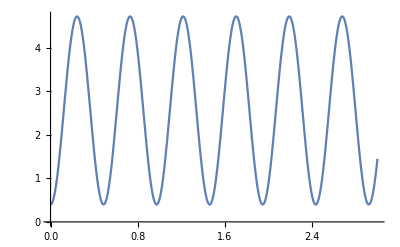

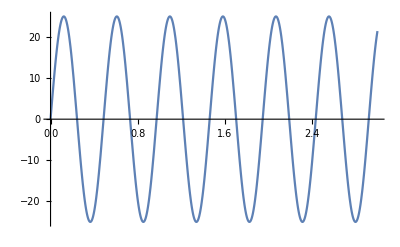

```mathematica
Plot[xt,{t,0,3}]
Plot[FNormal,{t,0,3}]
```

## Written Problems

-Graphics-